```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/pp/Documents/Repos/plant_hydro_standalone/appl

```mathematica
wI =Rest@Import["/Users/pp/Dropbox/UNI/Projekte/A08_Hydraulic_Standalone/Drougth_experiment_simulation/IO/Water_Input_type2.csv"];
(*wI =Rest@Import["/Users/pp/Dropbox/UNI/Projekte/A08_Hydraulic_Standalone/Drougth_experiment_simulation/IO/Water_Input_peak_rm.csv"];
```

```mathematica
wIs = wI[[1;;10225-1,1;;12]]
wIs//Length
```

{{2018-06-01 00:00:00,0.313025,0.312686,0.312345,0.312004,0.311663,0.311321,0.310978,0.310634,0.310291,0.309946,0.309601},10222,{2018-12-30 23:30:00,0.296717,0.272288,6,0.223865,0.215554,0.198124}}
 |  |  |  |

10224

```mathematica
swcraw= Import["/Users/pp/Dropbox/UNI/Projekte/A08_Hydraulic_Standalone/Drougth_experiment_simulation/IO/SWC_Inter.csv"];
forcingraw = Import["/Users/pp/Dropbox/UNI/Projekte/A08_Hydraulic_Standalone/Drougth_experiment_simulation/IO/Forcing_Inter.csv"];
```

```mathematica
forcingraw[[1]]
maxwsdown = 1040;
sw = Rest@forcingraw[[7249;;17473,{1,3}]];
vpd = Rest@forcingraw[[7249;;17473,{1,9}]];
Length[sw]
```

{dt,stn,swdown,tair,rainf,rh,wind,saturated_vapor_pressure_hPa,vpd,co2,air_temp_C_2100,air_humidity_%_2100,saturated_vapor_pressure_hPa_2100,VPD_kPa_2100,CO2_mean_ppm_2100,psurf}

10224

```mathematica
swc= Rest@swcraw[[All,  {1,2}]];
```

```mathematica
Length@sw == Length@swc
```

False

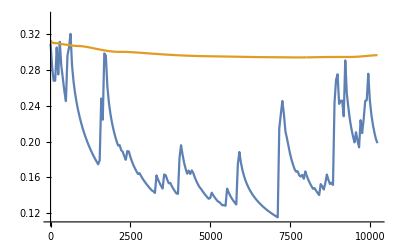

```mathematica
ListPlot[Table[θInt[i], {i,{1,11}}], Joined->True, PlotRange->{0.11, 0.34}]
```

```mathematica
rtβ = 0.96;
min = 0;
max  =100;
step = 10;

rootfracs = Table[(rtβ^u -rtβ^(u+step)),{u,min,max,step}];
rootfracs /=Total[rootfracs]
```

{0.338969,0.225358,0.149825,0.0996087,0.0662231,0.0440273,0.0292708,0.0194602,0.0129378,0.00860144,0.00571852}

```mathematica
Table[(u+step), {u,min,max,step}]
```

{10,20,30,40,50,60,70,80,90,100,110}

```mathematica
rootfracs[[1]]
```

0.338969

```mathematica
Block[{dmin = 00, dmax= 50},{(-#^dmax+#^dmin)/(-#^100+1)}&/@{0.96,0.97, 0.98, 0.99, 0.995}]
```

{{0.885045},{0.820974},{0.733047},{0.623051},{0.562331}}

```mathematica
dt =1800*48;
dt =1;

ηLS = 1.0;
h = 20.0;
ψH = 998* 9.81* h/2.0 /10^6;
Η = 1.0/3600.0;

ca  = 415;
p = 1.013* 10^5;
g0 = 0.005 * dt;
g1 = 1.5;

ψLclose50 = -2.1;
d50close = 10.0;

LAI = 4.8;
cLeaf = 1.0;
cStem = 200*1000/18.0;

kXylemSat = 300 * dt;

RAI = 24.0;


θS = 0.43;
b =4.5;
ψSref = -4.5*1000 *10^(-6);


ksoilsat =15*100/86400.0;
ksoilsat = 20/100/3600.0 *dt ;
sd = 0.1;


ψS0 = -0.3;
ψL0 = -1.0;


ksoil[i_,t_]:= ksoilsat * (θInt[i][t ]/θS)^(2 +3b);
ψsoil[i_, t_]:= ψSref* (θInt[i][t]/θS)^(-b);

Anetmax = 5.7;
anet = sw[[All,2]]/maxwsdown *Anetmax * dt;
anetInt = Interpolation[anet,InterpolationOrder->0];
vpdInt = Interpolation[vpd[[All,2]]*1000,InterpolationOrder->0];
Table[θInt[12-i]= Interpolation[wIs[[All,i+1]],InterpolationOrder->0], {i, 1, 11}];
```

```mathematica
J[ψS_, ψL_]:= (ψS - ψL
 -ψH)* kXylemSat* Η/(ηLS*h/2.0);
G[ψS_,t_]:= Sum[rootfracs[[i]]ksoil[i, t*dt/1800]*Sqrt[RAI]/π/sd* (ψsoil[i, t *dt/1800] - ψS -998*9.81*h/2/10^6)/9.81*10^6,{i,1,11}];
β[ψL_]:= 1/(1 + Exp[-d50close*(ψL-ψLclose50)]);
gs[ψL_, t_]:= g0 + β[ψL]*(1 + g1/Sqrt[vpdInt[t*dt/1800]/p])*anetInt[dt *t/1800]/ca;
T[ψL_, t_]:=gs[ψL, t]*LAI*vpdInt[t*dt/1800]/p


tmin = 1800/dt;
tmax = 1800/dt*48*20;


Timing[sol = NDSolve[{
cLeaf * ψL'[t] -J[ψS[t],ψL[t]]+T[ψL[t], t]==0,
cStem*h*Η * ψS'[t] -G[ψS[t], t]+J[ψS[t],ψL[t]]==0,
ψL[tmin]==ψL0,
ψS[tmin]==ψS0},{ψL, ψS},{t,tmin,tmax}]]
```

{13.1684,{{ψL→                                       6
InterpolatingFunction[{{1800., 1.728 10 }}, <>],ψS→                                       6
InterpolatingFunction[{{1800., 1.728 10 }}, <>]}}}

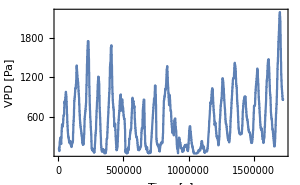
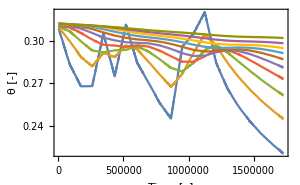
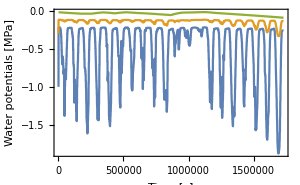
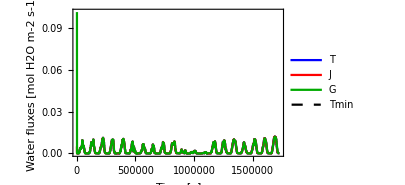
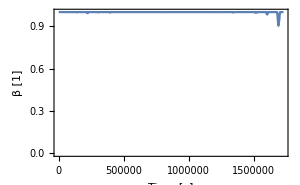
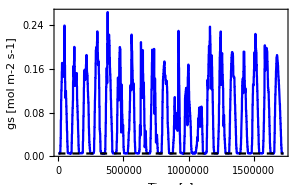
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[{{Plot[vpdInt[dt * x/1800],{x,tmin,tmax},PlotRange->All, ImageSize->300, Frame->True, FrameLabel->{"Time [s]","VPD [Pa]"}],Plot[Evaluate@Table[θInt[j][ dt * x/1800],{j,1,10}],{x,tmin,tmax}, ImageSize->300,PlotRange->All, Frame->True, FrameLabel->{"Time [s]","θ [-]"}]},{
Plot[{Evaluate[{ψL[x],ψS[x]}/.sol],ψsoil[1,dt * x/1800]},{x,tmin,tmax}, ImageSize->300,PlotRange->All, Frame->True, FrameLabel->{"Time [s]","Water potentials [MPa]"}],
Plot[Evaluate[{
T[ψL[x],x]/.sol ,
J[ψS[x],ψL[x]]/.sol,
G[ψS[x], x]/.sol,
T[-∞]}],{x,tmin,tmax},PlotRange-> {0,All}, Frame->True, FrameLabel->{"Time [s]","Water fluxes\n[mol H2O m-2 s-1]"},PlotStyle->{Blue,Red,Darker@Green,Directive[Black,Dashed]},
PlotLegends->{"T", "J", "G", "Tmin"}, ImageSize->300

]},
{
Plot[Evaluate[{β[ψL[x]]/.sol}],{x,tmin,tmax},PlotRange->{0,1}, ImageSize->300, Frame->True, FrameLabel->{"Time [s]","β [1]"}],

Plot[Evaluate[{gs[ψL[x], x]/.sol, g0}],{x,tmin,tmax}, ImageSize->300,PlotRange->All, Frame->True, FrameLabel->{"Time [s]","gs [mol m-2 s-1]"}, PlotStyle->{Blue,Directive[Black,Dashed],Directive[Black,Dashed]}]}}]
```

```mathematica
π0 = -2.1;
ϵ = 10;
tlp = 1/(1/ϵ+1/π0)
```

-2.65823

```mathematica
rwc[ψ_]:= Piecewise[{{
(π0 + ϵ+ ψ + Sqrt[(π0 + ϵ+ψ)^2-4 ϵ π0])/2/ϵ,


ψ>tlp},{π0/ψ,ψ<tlp}}]
```

```mathematica
vpdInt[30/30]
```

591.591

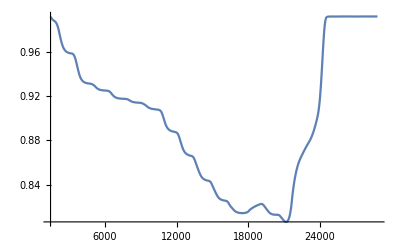

```mathematica
Plot[rwc[ψS[x]]/.sol, {x,tmin,tmax}]
```

```mathematica
kss = 4 mm/s
```

(4 mm)/s

```mathematica
kss = 4*dt
```

2400

```mathematica
x = {1,2,3}
```

{1,2,3}

```mathematica
Exp[x]
```

{ⅇ,ⅇ^2,ⅇ^3}

```mathematica
.10Exp[#]&/@ (1,2,3)
```

```mathematica
mat  = 48;
py = 11;
c = 0.05;
```

```mathematica
mat/c
```

960.

```mathematica
py/c
```

220.

```mathematica
10224/48
```

213

```mathematica
3
```

```mathematica
tmin = 48*200
tmax = 48*210
```

9600

10080

```mathematica
70
```

```mathematica
Table
```

```mathematica
kss = 4
```

4

```mathematica
10 * 1800
```

18000

```mathematica
10 /1000*86400/4000*40.0*4.8
```

41.472

```mathematica
1/0(1.0/20 +
```

```mathematica
431/10000.
```

0.0431

```mathematica
f[x_, slope_, psi50_]:= Exp[-  Exp[-slope(x- psi50 ) ]]
```

General::munfl: Exp[-2979.98] is too small to represent as a normalized machine number; precision may be lost.

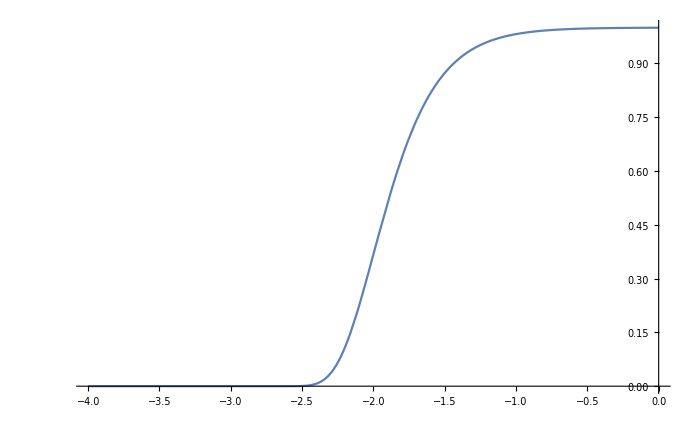

```mathematica
a =4;
psi = -2;
Plot[f[t,a,psi],{t,-4,0}, PlotRange->All]
```

```mathematica
`
```

```mathematica
N[f[-2.073302584116333,a,psi], 10]
```

0.261656

```mathematica
Solve[f[psi50,s,ψ]==1/2,ψ, Reals]
```

{{ψ→-(-psi50 s-Log[Log[2]])/s}}

```mathematica
FullSimplify[-(-psi50 s-Log[Log[2]])/s]
```

psi50+Log[Log[2]]/s

```mathematica
paramb =
```

```mathematica
N[f[-2,5,psi], 10]
```

0.3678794412

```mathematica
-2+Log[Log[2.]]/5
```

-2.0733

```mathematica
f[-2,5,-2+Log[Log[4]]/5]
```

1/4